#### Set plot styles and custom plot functions

```mathematica
SetOptions[#,Frame->True,FrameStyle->Directive[Black,18,FontFamily->Times,Thickness[.004]],AspectRatio->1,PlotStyle->Thick,ImageSize->400]&@{Plot,LogPlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot};
SetOptions[#,Frame->True,LabelStyle->Directive[Black,16,FontFamily->Times,Thickness[.004]],AspectRatio->1,ImageSize->400]&@{Histogram,MatrixPlot};
logSpace[a_, b_, n_] := 10.0^Range[Log10[a], Log10[b], (Log10[b] - Log10[a])/(n - 1)];

topLeft[x_] := Placed[x, {Scaled[{.38, .95}], {.9, 1}}];
topRight[x_] := Placed[x,{Scaled[{.95, .95}], {.9, 1}}];
Legend//Clear;
Legend[legendList_,opt:OptionsPattern[{Position->"Right",Type->"Line",LineLegend}]] := Module[{f},
If[OptionValue[Type]=="Line",
f=LineLegend;];
If[OptionValue[Type]=="Swatch",
f=SwatchLegend;];
If[OptionValue[Position]=="Right",
f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topRight//Return];
If[OptionValue[Position]=="Left",
f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topLeft//Return];
f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//Placed[#,OptionValue[Position]]&//Return;
];
LogTicks//Clear;
LogTicks[min_,max_,step_] := Block[{lmin, lmax, t},
   lmin = Floor[Log10[min]];
   lmax = Floor[Log10[max]];
   t=0;
   Return[{Join[
      Table[{10^i, If[Mod[++t,step]==0,Superscript[10, i],Null], {0.012, 0}}, {i, Floor[lmin], Ceiling[lmax]}], (Flatten[#1, 1] &)[
       Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], 
        Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]], 
     Join[Table[{10^i, Null, {0.012, 0}}, {i, Floor[lmin], 
     Ceiling[lmax]}], (Flatten[#1, 1] &)[ Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]]}  ]
];
LogTicks[min_, max_] := LogTicks[min,max,1];
```

### Constant

```mathematica
Ar40={"Ar",18,40,0};
Nucleus=Ar40;
Subscript[ϵ, χ]=10^-4;
Subscript[α, D]=0.5;
Subscript[g, D]=√(4π Subscript[α, D]);
gA=1.27;
mN=0.938;
mA=Nucleus⟦3⟧ mN;
AtomicNumber=Nucleus⟦2⟧;
Ji=Nucleus⟦4⟧;
GeVcm=(6.5821 10^-25) (3 10^10);
e=0.30282212;
```

### Read strengths

```mathematica
arStrengths=Import["ar40_s.res","Table"][[10;;209]];
arStrengths[[All,1]]-=arStrengths[[1,1]];
arStrengths[[All,1]]*=10^-3;
arStrengthsNon0=arStrengths//DeleteCases[#,_?(#[[2]]==0&)]&;

Print["ΔE [GeV], strength"]
arStrengthsNon0[[1;;20]]//MatrixForm
```

ΔE [GeV], strength

(0.00325988 | 0.06583
0.004639 | 0.00058
0.00524681 | 0.00277
0.00585763 | 0.00075
0.0086381 | 0.00007
0.00925304 | 0.00979
0.00994599 | 0.0177
0.0101513 | 0.02626
0.0108052 | 0.002
0.0110938 | 0.00377
0.0114019 | 0.01938
0.0115691 | 0.39735
0.011787 | 0.03552
0.0118216 | 0.00539
0.012356 | 0.01451
0.0124792 | 0.01051
0.0127116 | 0.02327
0.0128182 | 0.00791
0.0128567 | 0.18201
0.0131314 | 0.00215)

### Inelastic differential cross section

```mathematica
Subscript[p, χ][E_,mχ_]:=√(E^2-mχ^2);
```

```mathematica
l33[Eχ_,q_,ΔE_,mχ_]:=Max[1+1/(Eχ(Eχ-ΔE))(-3/2(Subscript[p, χ][Eχ,mχ])^2-3/2(Subscript[p, χ][Eχ-ΔE,mχ])^2+3/2 q^2-mχ^2/4),0];
ldotl[Eχ_,q_,ΔE_,mχ_]:=Max[3-1/(Eχ(Eχ-ΔE))(1/2((Subscript[p, χ][Eχ,mχ])^2+(Subscript[p, χ][Eχ-ΔE,mχ])^2-q^2)+3/4 mχ^2),0];
llterm[Eχ_,ER_,ΔE_,mχ_]:=Max[1/2(ldotl[Eχ,√(2mA ER),ΔE,mχ]-l33[Eχ,√(2mA ER),ΔE,mχ]),0];
```

```mathematica
(*mv is dark photon mass*)
dσdErGT0[ER_,Eχ_, mχ_,BGT_,ΔE_]:=If[Eχ>mχ+ΔE&&ErMinGT[Eχ,mχ,ΔE]< ER<ErMaxGT[Eχ,mχ,ΔE] ,(2 e^2 Subscript[ϵ, χ]^2 Subscript[g, D]^2 (Eχ-ER-ΔE)^2)/(Subscript[p, χ][Eχ,mχ]Subscript[p, χ][Eχ-ΔE-ER,mχ](2 mA ER+(3mχ)^2)^2)mA/(2π)(4π)/(2Nucleus⟦4⟧+1) (2 gA^2)/(6π)llterm[Eχ,ER,ΔE,mχ] BGT,0];(*this is for dσdEr plot*)

dσdErGT[ER_,Eχ_, mχ_,BGT_,ΔE_]:=If[Eχ>mχ+ΔE ,(2 e^2 Subscript[ϵ, χ]^2 Subscript[g, D]^2 (Eχ-ER-ΔE)^2)/(Subscript[p, χ][Eχ,mχ]Subscript[p, χ][Eχ-ΔE-ER,mχ](2 mA ER+(3mχ)^2)^2)mA/(2π)(4π)/(2Nucleus⟦4⟧+1) (2 gA^2)/(6π)llterm[Eχ,ER,ΔE,mχ]BGT,0];
```

### Elastic differential cross section

```mathematica
FHelm[A_,Er_]:=3(Sin[q r]-(q r)Cos[q r])/(q r)^3 Exp[(-(q s)^2)/2]/.{q->6.92 √A √Er,r->((1.23 A^(1/3)-.6)^2+7/3 π^2(0.52)^2-5(0.9)^2)^(1/2),s->0.9};
dσdErEl[ER_,Eχ_, mχ_]:=(e^2 Subscript[ϵ, χ]^2 Subscript[g, D]^2 AtomicNumber^2)/(4π (Subscript[p, χ][Eχ,mχ])^2(2 mA ER+(3mχ)^2)^2)(2 Eχ^2 mA(1-ER/Eχ-(mA ER)/(2 Eχ^2))+mA ER^2 ) FHelm[Nucleus⟦3⟧ ,ER]^2;
```

### |cosθ|<1 constraint

```mathematica
ErTolerance=.005;(*to avoid numerical error and imaginary number*)
ErMaxEl[Eχ_,mχ_]:=(2 Subscript[p, χ][Eχ,mχ]Subscript[p, χ][Eχ,mχ])/mA(1-ErTolerance);
ErMaxGT[Eχ_,mχ_,ΔE_]:=(Subscript[p, χ][Eχ,mχ]+Subscript[p, χ][Eχ-ΔE,mχ])^2/(2mA)(1-ErTolerance);
ErMinGT[Eχ_,mχ_,ΔE_]:=(Subscript[p, χ][Eχ,mχ]-Subscript[p, χ][Eχ-ΔE,mχ])^2/(2mA)(1+ErTolerance);
```

```mathematica
dσdErGTsum0[ER_,Eχ_,mχ_]:=If[Eχ>mχ,Sum[dσdErGT0[ER,Eχ,mχ,arStrengthsNon0[[ii,2]],arStrengthsNon0[[ii,1]]],{ii,1,Length[arStrengthsNon0]}],0];
```

```mathematica
mχMeV=30;
EχMeV=75;
pointsGTEr=Table[{ErkeV,10^-6 GeVcm^2  dσdErGTsum0[ErkeV 10^-6,EχMeV 10^-3,mχMeV 10^-3]},{ErkeV,1,250}];
pointsElEr=Table[{ErkeV,10^-6 GeVcm^2 dσdErEl[ErkeV 10^-6, EχMeV 10^-3,mχMeV 10^-3]},{ErkeV,1,250}];
```

```mathematica
Export["ar40_DM_Er_el.csv",pointsElEr];
Export["ar40_DM_Er_inel.csv",pointsGTEr];
```

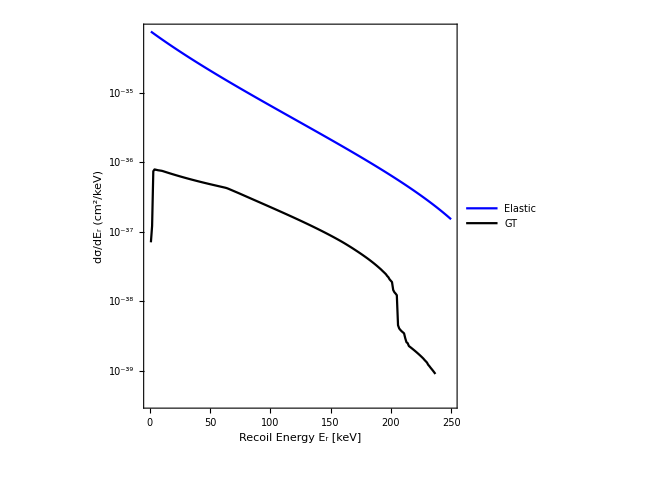

```mathematica
ListLogPlot[{pointsElEr,pointsGTEr},Joined->True,PlotStyle->{ Blue,Black},PlotLegends->Legend[{"Elastic","GT"},Position->{0.15,0.12},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Black]&)],FrameLabel->{"Recoil Energy E_r [keV]", "dσ/dE_r (cm^2/keV)"}]
```

### Total cross section

```mathematica
σGT[Eχ_,mχ_,BGT_,ΔE_]:=If[Eχ>ΔE+mχ,NIntegrate[dσdErGT[ER,Eχ,mχ,BGT,ΔE],{ER,ErMinGT[Eχ,mχ,ΔE],ErMaxGT[Eχ,mχ,ΔE]}],0];
σGTsum[Eχ_,mχ_]:=Sum[σGT[Eχ,mχ,arStrengthsNon0[[ii,2]],arStrengthsNon0[[ii,1]]],{ii,1,Length[arStrengthsNon0]}];
σ1stGT[Eχ_,mχ_]:=σGT[Eχ,mχ,arStrengthsNon0[[1,2]],arStrengthsNon0[[1,1]]];
σEl[Eχ_,mχ_]:=If[Eχ>mχ, NIntegrate[dσdErEl[ER,Eχ,mχ],{ER,0,ErMaxEl[Eχ,mχ]}],0];
```

## Plots (σ [cm^2], E_χ [MeV])

### m_χ= 30 MeV

```mathematica
mχMeV=30;
mχ=mχMeV 10^-3;
pointsGT=Table[{EχMeV,GeVcm^2  σGTsum[EχMeV 10^-3,mχ]},{EχMeV,mχMeV,100}];
points1stGT=Table[{EχMeV,GeVcm^2  Re[σ1stGT[EχMeV 10^-3,mχ]]},{EχMeV,mχMeV,100}];
pointsEl=Table[{EχMeV,GeVcm^2 σEl[EχMeV 10^-3,mχ]},{EχMeV,mχMeV,100}];
```

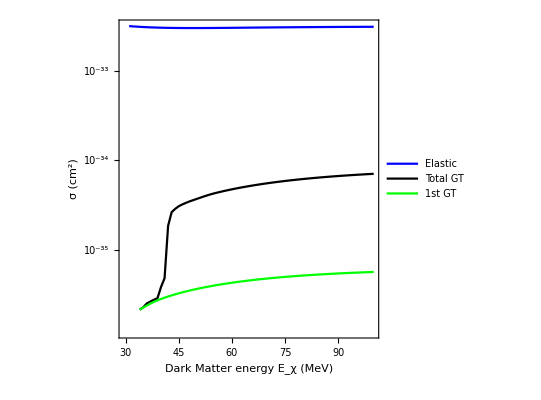

```mathematica
ListLogPlot[{pointsEl,pointsGT,points1stGT},Joined->True,PlotStyle->{Blue,Black,Green},PlotLegends->Legend[{"Elastic","Total GT","1st GT"},Position->{0.8,0.15},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Black]&)],FrameLabel->{"Dark Matter energy E_χ (MeV)", "σ (cm^2)"},FrameTicks->{LogTicks[10^-35,10^-31,1],Automatic}]
```

```mathematica
points1stGT
```

{{30,0.},{31,0.},{32,0.},{33,0.},{34,2.12544×10^-36},{35,2.24531×10^-36},{36,2.36495×10^-36},{37,2.48441×10^-36},{38,2.59879×10^-36},{39,2.70336×10^-36},{40,2.80151×10^-36},{41,2.89504×10^-36},{42,2.985×10^-36},{43,3.072×10^-36},{44,3.15643×10^-36},{45,3.23855×10^-36},{46,3.31854×10^-36},{47,3.39652×10^-36},{48,3.47259×10^-36},{49,3.54682×10^-36},{50,3.61925×10^-36},{51,3.68994×10^-36},{52,3.75893×10^-36},{53,3.82625×10^-36},{54,3.89192×10^-36},{55,3.95599×10^-36},{56,4.01847×10^-36},{57,4.0794×10^-36},{58,4.1388×10^-36},{59,4.19671×10^-36},{60,4.25314×10^-36},{61,4.30813×10^-36},{62,4.36171×10^-36},{63,4.4139×10^-36},{64,4.46473×10^-36},{65,4.51423×10^-36},{66,4.56243×10^-36},{67,4.60935×10^-36},{68,4.65504×10^-36},{69,4.6995×10^-36},{70,4.74278×10^-36},{71,4.7849×10^-36},{72,4.82588×10^-36},{73,4.86576×10^-36},{74,4.90456×10^-36},{75,4.94232×10^-36},{76,4.97905×10^-36},{77,5.01478×10^-36},{78,5.04954×10^-36},{79,5.08336×10^-36},{80,5.11625×10^-36},{81,5.14825×10^-36},{82,5.17937×10^-36},{83,5.20964×10^-36},{84,5.23909×10^-36},{85,5.26774×10^-36},{86,5.2956×10^-36},{87,5.3227×10^-36},{88,5.34906×10^-36},{89,5.37471×10^-36},{90,5.39965×10^-36},{91,5.42392×10^-36},{92,5.44752×10^-36},{93,5.47049×10^-36},{94,5.49283×10^-36},{95,5.51456×10^-36},{96,5.5357×10^-36},{97,5.55628×10^-36},{98,5.57629×10^-36},{99,5.59577×10^-36},{100,5.61472×10^-36}}

```mathematica
Export["1stDMGT.csv",points1stGT];
Export["totalDMGT.csv",pointsGT];
Export["ar40_DM_inel.csv",pointsGT];
```

## Dark matter flux

### Detector specs

```mathematica
Subscript[N, A]=6 10^23;
yearsCsI=1.61;
yearsLAr=0.6;
yearsCCM=3;

massCsI=14.6;(*kg*)
massLAr=24.4;
massCCM=7000;

DistanceCsI=19.3 10^2; (*cm*)
DistanceLAr=28.4 10^2;
DistanceCCM=20 10^2;

pionRatioCOHERENT=0.0803;
pionRatioCCM=0.052;

POTCsI=3.2 10^23; (*total*)
POTLAr=1.34 10^23;
POTCCM=10^22*yearsCCM;

secCsI=yearsCsI*365*24*60^2;
secLAr=yearsLAr*365*24*60^2;
secCCM=yearsCCM*365*24*60^2;

(*cm^-2 s^-1*)
FluxCsI=POTCsI pionRatioCOHERENT  / (4π DistanceCsI^2 secCsI);
FluxLAr=POTLAr pionRatioCOHERENT / (4π DistanceLAr^2 secLAr) ;
FluxCCM=POTCCM pionRatioCCM / (4π DistanceCCM^2 secCCM) ;

ExposureCsI=massCsI yearsCsI*365; (*kg days*)
ExposureLAr=massLAr yearsLAr*365;
ExposureCCM=massCCM yearsCCM*365;
```

```mathematica
ExposureCCM
FluxCCM
```

7665000

328040.

```mathematica
(*channels: pi0, pim, brem*)
DMFluxdata=Import["ccm_flux/pi0_90.csv"];
FluxenergyMeV=DMFluxdata[[All,1]]; 
Fluxweight=DMFluxdata[[All,2]];
Fluxnum=99;
Subscript[m, V]=90 10^-3; (*GeV*)
Subscript[m, χ]=Subscript[m, V]/3;
```

### Dark matter Rate (per sec) at CCM LAr

```mathematica
prefactorCCM=Subscript[ϵ, χ]^2 FluxCCM ExposureCCM(10^3 Subscript[N, A])/Nucleus⟦3⟧60^2*24  GeVcm^2;

RateEl=prefactorCCM∑_(i=1)^Fluxnum Fluxweight⟦i⟧ σEl[FluxenergyMeV⟦i⟧ 10^-3,Subscript[m, χ]]
RateInel=prefactorCCM∑_(i=1)^Fluxnum Fluxweight⟦i⟧Re[σGTsum[FluxenergyMeV⟦i⟧ 10^-3,Subscript[m, χ]]]
```

99.2328

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ER near {ER} = {0.0000205352}. NIntegrate obtained 2.20068×10^-11-1.33498×10^-11 ⅈ and 2.73233×10^-13 for the integral and error estimates.

1.59779

```mathematica
RateEl*(FluxLAr ExposureLAr)/(FluxCCM ExposureCCM)
RateInel*(FluxLAr ExposureLAr)/(FluxCCM ExposureCCM)
```

1.18322

0.0190515

```mathematica
RateEl/RateInel
```

62.1064